```mathematica
Binomial[n,k]
```

Binomial[n,k]

```mathematica
Binomial[4,2]
```

6

```mathematica
FunctionExpand@Binomial[n,k]
```

Gamma[1+n]/(Gamma[1+k] Gamma[1-k+n])

```mathematica
DiscretePlot3D[Gamma[1+n]/(Gamma[1+k] Gamma[1-k+n]),{k,1,20},{n,1,20}]
```

-Graphics3D-

```mathematica
Plot3D[Gamma[1+n]/(Gamma[1+k] Gamma[1-k+n]),{k,1,20},{n,1,20}]
```

-Graphics3D-

```mathematica
Composition[a,b,c]
```

a@*b@*c

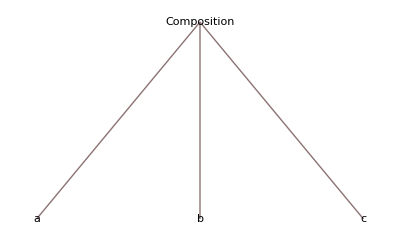

```mathematica
TreeForm@
Composition[a,b,c]
```

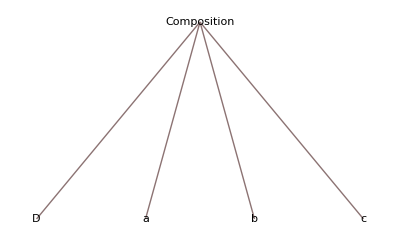

```mathematica
TreeForm@
Composition[D,a,b,c]
```

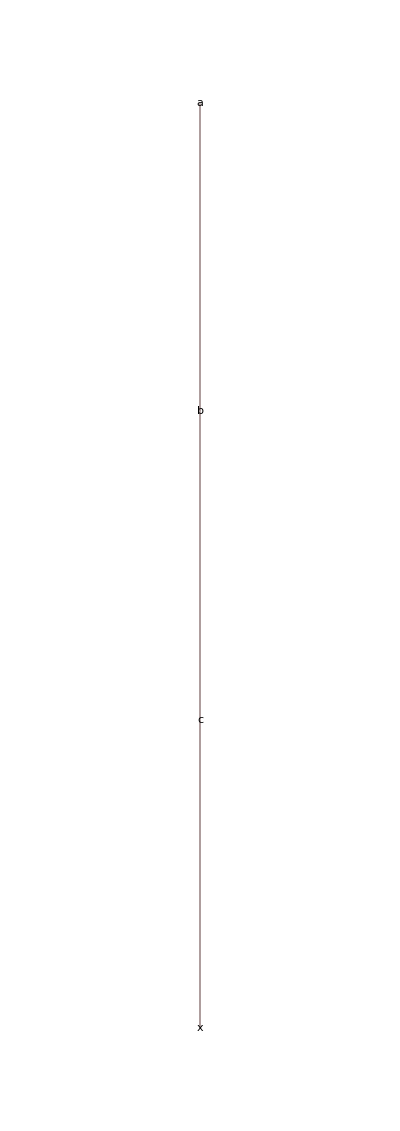

```mathematica
TreeForm@
Composition[a,b,c][x]
```

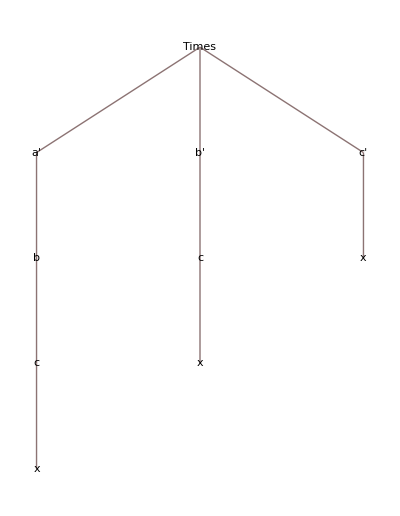

```mathematica
TreeForm@
Composition[D[#,x]&,a,b,c][x]
```

```mathematica
D[Composition[a,b,c][x],x]
```

a'[b[c[x]]] b'[c[x]] c'[x]

```mathematica
D[Composition[a,b,c][x],x]==Composition[D[#,x]&,a,b,c][x]
```

True

```mathematica
Equal[1,1,1]
```

True

```mathematica
Apply[
Equal,{
D[Composition[a,b,c][x],x],
Composition[D[#,x]&,a,b,c][x],
Composition[a',D[#,x]&,b,c][x]
}]
```

a'[b[c[x]]] b'[c[x]] c'[x]==a'[b[c[x]]] b'[c[x]] c'[x]==a'[b'[c[x]] c'[x]]

```mathematica
D[f[g[x]],x]
```

f'[g[x]] g'[x]

```mathematica
InputForm@f'[g[x]] g'[x]
```

Derivative[1][f][g[x]] g'[x]

```mathematica
FullForm@f'[g[x]] g'[x]
```

Derivative[1][f][g[x]] g'[x]

```mathematica
2x+1
```

1+2 x

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

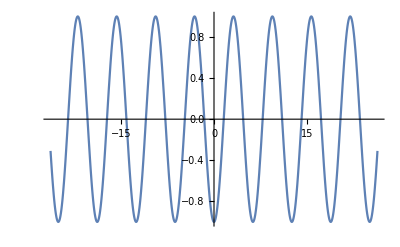

```mathematica
Plot[-Cos[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Grad[x^2-λ(x-2),{x,λ}]
```

{2 x-λ,2-x}

```mathematica
Solve[{2 x-λ==0,2-x==0},{x,λ}]
```

{{x→2,λ→4}}

```mathematica
Grad[x^2-λ(x-4),{x,λ}]
```

{2 x-λ,4-x}

```mathematica
Solve[{2 x-λ==0,4-x==0},{x,λ}]
```

{{x→4,λ→8}}

```mathematica
Grad[x^2-λ(y-x^2),{x,y,λ}]
```

{2 x+2 x λ,-λ,x^2-y}

```mathematica
Solve[{2 x+2 x λ==0,-λ==0,x^2-y==0},{x,y,λ}]
```

{{x→0,y→0,λ→0}}

```mathematica
Grad[√(1+y'[x]^2),x]
```

√(1+y'[x]^2)x

```mathematica
Grad[√(1+y'[x]^2),{x,y[x]}]
```

{(y'[x] y''[x])/(√(1+y'[x]^2)),0}

```mathematica
D[F[x,y,y'], ϵ]
```

0

```mathematica
D[F[x,y[ϵ],y'[ϵ]], ϵ]
```

y''[ϵ] F^(0,0,1)[x,y[ϵ],y'[ϵ]]+y'[ϵ] F^(0,1,0)[x,y[ϵ],y'[ϵ]]

```mathematica
SurfaceData["Sphere","Properties"]
```

{algebraic degree,algebraic equation,alternate names,area element,associated people,Cartesian equation,centroid of solid,Christoffel symbol of the second kind,(map) chromatic number,classes,cross sections,entity classes,Euler characteristic,filled region,coefficients of the first fundamental form,Gaussian curvature,generalized diameter,genus,3-D graphics,image,implicit Gaussian curvature,implicit mean curvature,implicit normal vector,moment of inertia tensor of solid,CDF of lengths,mean line segment length,PDF of lengths,mean curvature,metric tensor,name,number of nodes,normal vector,parameters,parametric equations,principal curvatures,number of punctures,related Wolfram Language symbols,Ricci tensor,Riemann tensor,coefficients of the second fundamental form,semialgebraic description,singular points,sport objects,surface area,variable constraints,variable descriptions,variables,vector length,volume of solid}

```mathematica
ArcCurvature[{x,x^2},x]
```

2/((1+4 x^2)^(3/2))

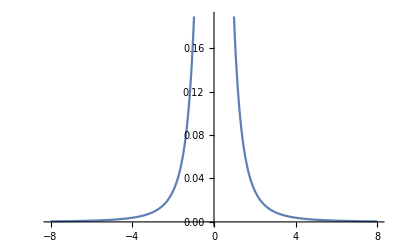

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-8,8}]
```

```mathematica
Integrate[2/((1+4 x^2)^(3/2)),x]
```

(2 x)/(√(1+4 x^2))

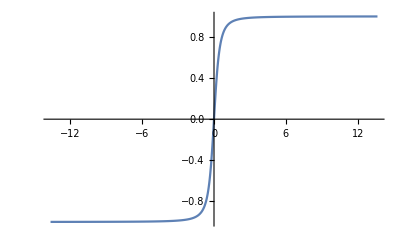

```mathematica
Plot[(2 x)/(√(1+4 x^2)),{x,-13.649999999999999,13.649999999999999}]
```

```mathematica
Integrate[D[(2 x)/(√(1+4 x^2)),x],{x,-1,1}]
```

4/(√5)

```mathematica
N[4/(√5)]
```

1.78885

```mathematica
Integrate[D[(2 x)/(√(1+4 x^2)),x],{x,-1,1}]/2
```

2/(√5)

```mathematica
N[2/(√5)]
```

0.894427

```mathematica
With[{a=-1,b=1},
Integrate[D[(2 x)/(√(1+4 x^2)),x],{x,a,b}]/Abs[a-b]
]
```

2/(√5)

```mathematica
Manipulate[
Integrate[D[(2 x)/(√(1+4 x^2)),x],{x,-a,a}]/(2a)
,{a,10,.1}]
```

```mathematica
Limit[Integrate[D[(2 x)/(√(1+4 x^2)),x],{x,-a,a}]/(2a),a->0]
```

2

```mathematica
SurfaceData["Sphere",EntityProperty["Surface","FirstFundamentalForm"]]
```

Function[a,Function[{u,v},a^2 {Sin[v]^2,0,1}]]

```mathematica
SurfaceData["Sphere","ParametricEquations"]
```

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1]
```

Function[{u$,v$},1 {Cos[u$] Sin[v$],Sin[u$] Sin[v$],Cos[v$]}]

```mathematica
Function[{u$,v$},1 {Cos[u$] Sin[v$],Sin[u$] Sin[v$],Cos[v$]}][u,v]
```

{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}

```mathematica
Grad[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,v}]
```

{{-Sin[u] Sin[v],Cos[u] Cos[v]},{Cos[u] Sin[v],Cos[v] Sin[u]},{0,-Sin[v]}}

```mathematica
Transpose[{{-Sin[u] Sin[v],Cos[u] Cos[v]},{Cos[u] Sin[v],Cos[v] Sin[u]},{0,-Sin[v]}}]
```

{{-Sin[u] Sin[v],Cos[u] Sin[v],0},{Cos[u] Cos[v],Cos[v] Sin[u],-Sin[v]}}

```mathematica
MatrixForm[{{-Sin[u] Sin[v],Cos[u] Cos[v]},{Cos[u] Sin[v],Cos[v] Sin[u]},{0,-Sin[v]}}]
```

(-Sin[u] Sin[v] | Cos[u] Cos[v]
Cos[u] Sin[v] | Cos[v] Sin[u]
0 | -Sin[v])

```mathematica
Transpose[Grad[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,v}]]
```

{{-Sin[u] Sin[v],Cos[u] Sin[v],0},{Cos[u] Cos[v],Cos[v] Sin[u],-Sin[v]}}

```mathematica
{-Sin[u] Sin[v],Cos[u] Sin[v],0}.{-Sin[u] Sin[v],Cos[u] Sin[v],0}
```

Cos[u]^2 Sin[v]^2+Sin[u]^2 Sin[v]^2

```mathematica
Table[a.b,
{a,{-Sin[u] Sin[v],Cos[u] Sin[v],0}},
{b,{Cos[u] Cos[v],Cos[v] Sin[u],-Sin[v]}}
]
```

{{(-Sin[u] Sin[v]).(Cos[u] Cos[v]),(-Sin[u] Sin[v]).(Cos[v] Sin[u]),(-Sin[u] Sin[v]).(-Sin[v])},{(Cos[u] Sin[v]).(Cos[u] Cos[v]),(Cos[u] Sin[v]).(Cos[v] Sin[u]),(Cos[u] Sin[v]).(-Sin[v])},{0.(Cos[u] Cos[v]),0.(Cos[v] Sin[u]),0.(-Sin[v])}}

```mathematica
MatrixForm[%53]
```

((-Sin[u] Sin[v]).(Cos[u] Cos[v]) | (-Sin[u] Sin[v]).(Cos[v] Sin[u]) | (-Sin[u] Sin[v]).(-Sin[v])
(Cos[u] Sin[v]).(Cos[u] Cos[v]) | (Cos[u] Sin[v]).(Cos[v] Sin[u]) | (Cos[u] Sin[v]).(-Sin[v])
0.(Cos[u] Cos[v]) | 0.(Cos[v] Sin[u]) | 0.(-Sin[v]))

```mathematica
Table[a.b,
{a,{{-Sin[u] Sin[v],Cos[u] Sin[v],0},{Cos[u] Cos[v],Cos[v] Sin[u],-Sin[v]}}},
{b,{{-Sin[u] Sin[v],Cos[u] Sin[v],0},
{Cos[u] Cos[v],Cos[v] Sin[u],-Sin[v]}}}
]
```

{{Cos[u]^2 Sin[v]^2+Sin[u]^2 Sin[v]^2,0},{0,Cos[u]^2 Cos[v]^2+Cos[v]^2 Sin[u]^2+Sin[v]^2}}

```mathematica
Table[FullSimplify[a.b,Element[u|v,Reals]],
{a,{{-Sin[u] Sin[v],Cos[u] Sin[v],0},{Cos[u] Cos[v],Cos[v] Sin[u],-Sin[v]}}},
{b,{{-Sin[u] Sin[v],Cos[u] Sin[v],0},
{Cos[u] Cos[v],Cos[v] Sin[u],-Sin[v]}}}
]
```

{{Sin[v]^2,0},{0,1}}

```mathematica
MatrixForm[{{Sin[v]^2,0},{0,1}}]
```

(Sin[v]^2 | 0
0 | 1)

```mathematica
ds^2==E du^2+2F du dv+G dv^2
```

ds^2==du^2 ⅇ+2 du dv F+dv^2 G

```mathematica
D[f[x,y],t]
```

0

```mathematica
D[f[x[t],y[t]],t]
```

y'[t] f^(0,1)[x[t],y[t]]+x'[t] f^(1,0)[x[t],y[t]]

```mathematica
x^2==mx+b
```

x^2==b+mx

```mathematica
Reduce[x^2==b+mx]
```

b==-mx+x^2

```mathematica
Solve[x^2==b+mx,{x},Reals]
```

{{x→ConditionalExpression[-√(b+mx), b+mx>0]},{x→ConditionalExpression[√(b+mx), b+mx>0]}}

```mathematica
x^2==b+m x
```

x^2==b+m x

```mathematica
Solve[x^2==b+m x,{x},Reals]
```

{{x→ConditionalExpression[m/2-1/2 √(4 b+m^2), 4 b+m^2>0]},{x→ConditionalExpression[m/2+1/2 √(4 b+m^2), 4 b+m^2>0]}}

```mathematica
AddSides[x^2==b+m x,-mx]
```

-mx+x^2==b-mx+m x

```mathematica
Reduce[-mx+x^2==b-mx+m x]
```

b==-m x+x^2

```mathematica
-mx+x^2==b-mx+m x
```

```mathematica
Reduce[-m x+x^2==b-m x+m x]
```

b==-m x+x^2

```mathematica
AddSides[x^2==b+m x,-m x]
```

-m x+x^2==b

```mathematica
Solve[x^2-m x+b==(x-a)^2,b]
```

{{b→a^2-2 a x+m x}}

```mathematica
Expand@((x-a)^2)
```

a^2-2 a x+x^2

```mathematica
m==2a
```

m==2 a

```mathematica
Expand@((x-m/2)^2)
```

m^2/4-m x+x^2

```mathematica
AddSides[AddSides[x^2==b+m x,-m x],m^2/4]
```

m^2/4-m x+x^2==b+m^2/4

```mathematica
(x-m/2)^2==b+m^2/4
```

(-m/2+x)^2==b+m^2/4

```mathematica
Solve[(-m/2+x)^2==b+m^2/4,{x},Reals]
```

{{x→ConditionalExpression[m/2-1/2 √(4 b+m^2), 4 b+m^2>0]},{x→ConditionalExpression[m/2+1/2 √(4 b+m^2), 4 b+m^2>0]}}

```mathematica
Solve[(-m/2+x)^2==b+m^2/4,x]
```

{{x→1/2 (m-√(4 b+m^2))},{x→1/2 (m+√(4 b+m^2))}}

```mathematica
f'[x]
```

f'[x]

```mathematica
Integrate[f'[x],x]
```

f[x]

```mathematica
x^2==x-1
```

x^2==-1+x

```mathematica
Reduce[x^2==-1+x]
```

x==(-1)^(1/3)||x==-(-1)^(2/3)

```mathematica
FindInstance[x==(-1)^(1/3)||x==-(-1)^(2/3),{x}]
```

{{x→(-1)^(1/3)}}

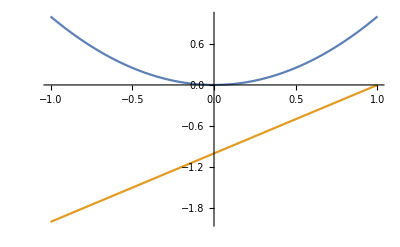

```mathematica
Plot[{x^2,x-1},{x,-1,1}]
```

```mathematica
D[x^2,x]==1
```

2 x==1

```mathematica
Reduce[2 x==1]
```

x==1/2

```mathematica
Solve[2 x==1,{x},Reals]
```

{{x→1/2}}

```mathematica
x^2==x-1
```

x^2==-1+x

```mathematica
Reduce[x^2==-1+x]
```

x==(-1)^(1/3)||x==-(-1)^(2/3)

```mathematica
Solve[x^2==-1+x,{x},Reals]
```

{}

```mathematica
Solve[x^2==-1+x,{x},Complexes]
```

{{x→(-1)^(1/3)},{x→-(-1)^(2/3)}}

```mathematica
N@((-1)^(1/3))
```

0.5+0.866025 ⅈ

```mathematica
Arg[0.5000000000000001+0.8660254037844386 ⅈ]
```

1.0472

```mathematica
-(-1)^(2/3)
```

-(-1)^(2/3)

```mathematica
N[-(-1)^(2/3)]
```

0.5-0.866025 ⅈ

```mathematica
I
```

ⅈ

```mathematica
I I
```

-1

```mathematica
x^3==p x + q
```

x^3==q+p x

```mathematica
Solve[x^3==q+p x,{x},Reals]
```

```mathematica
{{x->ConditionalExpression[Root[-q-p #1+#1^3&,1], (p>0&&q>(2 √(p^3))/(3 √3))||(-(2 √(p^3))/(3 √3)<q<(2 √(p^3))/(3 √3)&&p>0)||(q<-(2 √(p^3))/(3 √3)&&p>0)||p<0]},{x->ConditionalExpression[Root[-q-p #1+#1^3&,2], -(2 √(p^3))/(3 √3)<q<(2 √(p^3))/(3 √3)&&p>0]},{x->ConditionalExpression[Root[-q-p #1+#1^3&,3], -(2 √(p^3))/(3 √3)<q<(2 √(p^3))/(3 √3)&&p>0]}}
```

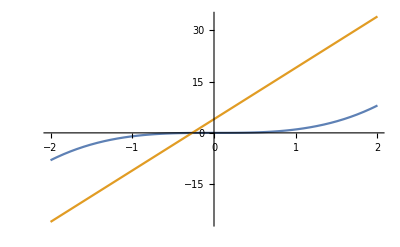

```mathematica
Plot[{x^3,15 x+4},{x,-2,2}]
```

```mathematica
(Re[3]+Im[4])/(Re[-1]+Im[7])
```

-3

```mathematica
(3+4 ⅈ)/(-1+7ⅈ)
```

1/2-ⅈ/2

```mathematica
N[1/2-ⅈ/2]
```

0.5-0.5 ⅈ

```mathematica
Factorial[n]+8==2^k∧{n,k}∈
```

8+n!==2^k&&(n|k)∈ℝ&&n>0&&k>0

```mathematica
Reduce[Factorial[n]+8==2^k,{n,k},]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[8+n!==2^k,{n,k},]

```mathematica
Solve[Factorial[n]+8==2^k,{n,k},]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[8+n!==2^k,{n,k},]

```mathematica
SolveAlways[Factorial[n]+8==2^k,{n,k},]
```

SolveAlways::argrx: SolveAlways called with 3 arguments; 2 arguments are expected.

SolveAlways[8+n!==2^k,{n,k},]

```mathematica
(a+b ⅈ)^(1/3)
```

(a+ⅈ b)^(1/3)